```mathematica
Needs["PlotLegends`"];
SetOptions[ListPlot,BaseStyle->{FontFamily->"Times",FontSize->14}];
tabler={};
I0=100*10^(-6);ϕ0=2.067833636*10^(-15);L=28*10^(-12);b=ϕ0/2/π/L/I0;
u[x_,y_,s_,yb_,αl_,αi_,b_]:=-s*x-s*αl*y+b(y-yb)^2-b*yb^2-Cos[x]*Cos[y]-αi*Sin[x]*Sin[y];
drawp[s_,yb_,αl_,αi_,b_]:=Plot3D[u[x,y,s,yb,αl,αi,b],{x,0,20},{y,-3,3},AxesLabel->{Style[x,14],Style[y,14],Style["U(x,y)",14]}];
Icflux[αl_,αi_,b_,si_,xi1_,yi1_,xi2_,yi2_,cl_,shift_]:=Module[{xf,yf,sf=si,i,u0,table0,P1,yb,N0,a,x,y,s},
u0[x_,y_]:=u[x,y,s,yb,αl,αi,b];
table0={};
N0=101;
xf=xi1;yf=yi1;sf=si;
For[i=0,i≤N0,i++,
yb=i*0.005*π+shift;
a=FindRoot[{D[u0[x,y],x]==0,D[u0[x,y],y]==0,D[D[u0[x,y],x],x]*D[D[u0[x,y],y],y]-(D[D[u0[x,y],x],y])^2==0},{{s,sf},{x,xf},{y,yf}}];
xf=x/.a;yf=y/.a;sf=s/.a;
table0=Prepend[table0,{yb/π,Abs[s/.a]*I0*10^6}];
table1=Prepend[table1,{yb/π,Abs[s/.a],xf,yf}];
];
xf=xi1;yf=yi1;sf=si;
For[i=0,i≥-N0,i--,
yb=i*0.005*π+shift;
a=FindRoot[{D[u0[x,y],x]==0,D[u0[x,y],y]==0,D[D[u0[x,y],x],x]*D[D[u0[x,y],y],y]-(D[D[u0[x,y],x],y])^2==0},{{s,sf},{x,xf},{y,yf}}];
xf=x/.a;yf=y/.a;sf=s/.a;
table0=Prepend[table0,{yb/π,Abs[s/.a]*I0*10^6}];
table1=Prepend[table1,{yb/π,Abs[s/.a],xf,yf}];
];
xf=xi2;yf=yi2;sf=si;
For[i=0,i≤N0,i++,
yb=i*0.005*π+π+shift;
a=FindRoot[{D[u0[x,y],x]==0,D[u0[x,y],y]==0,D[D[u0[x,y],x],x]*D[D[u0[x,y],y],y]-(D[D[u0[x,y],x],y])^2==0},{{s,sf},{x,xf},{y,yf}}];
xf=x/.a;yf=y/.a;sf=s/.a;
table0=Prepend[table0,{yb/π,Abs[s/.a]*I0*10^6}];
table1=Prepend[table1,{yb/π,Abs[s/.a],xf,yf}];
];
xf=xi2;yf=yi2;sf=si;
For[i=0,i≥-N0,i--,
yb=i*0.005*π+π+shift;
a=FindRoot[{D[u0[x,y],x]==0,D[u0[x,y],y]==0,D[D[u0[x,y],x],x]*D[D[u0[x,y],y],y]-(D[D[u0[x,y],x],y])^2==0},{{s,sf},{x,xf},{y,yf}}];
xf=x/.a;yf=y/.a;sf=s/.a;
table0=Prepend[table0,{yb/π,Abs[s/.a]*I0*10^6}];
table1=Prepend[table1,{yb/π,Abs[s/.a],xf,yf}];
];
Export["aa.txt",table1,"Table"];
tabler=table0;
P1=ListPlot[table0,PlotStyle->Directive[cl,PointSize[0.005]],GridLines->Automatic,Frame->True,ImageSize->800]
];
cri:=D[D[u[x,y,s,yb,0,0.3,b],x],x]+D[D[u[x,y,s,yb,0,0,b],y],y];
line=Line[{{0,0},{3,0}}]
Line[{{0,0},{3,0}}]
```

LegendPosition::shdw: Symbol LegendPosition appears in multiple contexts PlotLegends`Global`; definitions in context PlotLegends` may shadow or be shadowed by other definitions.

LegendShadow::shdw: Symbol LegendShadow appears in multiple contexts PlotLegends`Global`; definitions in context PlotLegends` may shadow or be shadowed by other definitions.

LegendSize::shdw: Symbol LegendSize appears in multiple contexts PlotLegends`Global`; definitions in context PlotLegends` may shadow or be shadowed by other definitions.

ShowLegend::shdw: Symbol ShowLegend appears in multiple contexts PlotLegends`Global`; definitions in context PlotLegends` may shadow or be shadowed by other definitions.

Line[{{0,0},{3,0}}]

Line[{{0,0},{3,0}}]

Prepend::normal: Nonatomic expression expected at position 1 in Prepend[table1, {0, 1.`, 14.137166941154069`, 0.`}].

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

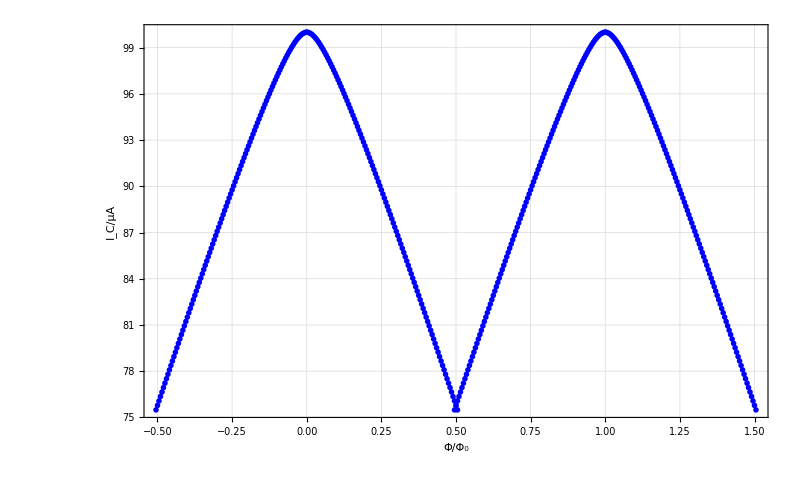

```mathematica
P1=Icflux[0,0,b,1,13.5,0,3,3,Blue,0];
ShowLegend[Show[P1,FrameLabel->{"Φ/Φ_0","I_C/μA"}],{{{Graphics[{Blue,line}],Style["L=28pH",14]}},LegendPosition->{1.1,-0.2},LegendShadow->None,LegendSize->0.35}]
```

```mathematica
tabler=tabler[[All,2]];
m=Max[tabler];
n=Min[tabler];
r=(m-n)
```

24.5113

```mathematica
For[i=1;r=0,i≤100,r=r+i;i=i+1]
```

```mathematica
r
```

5050

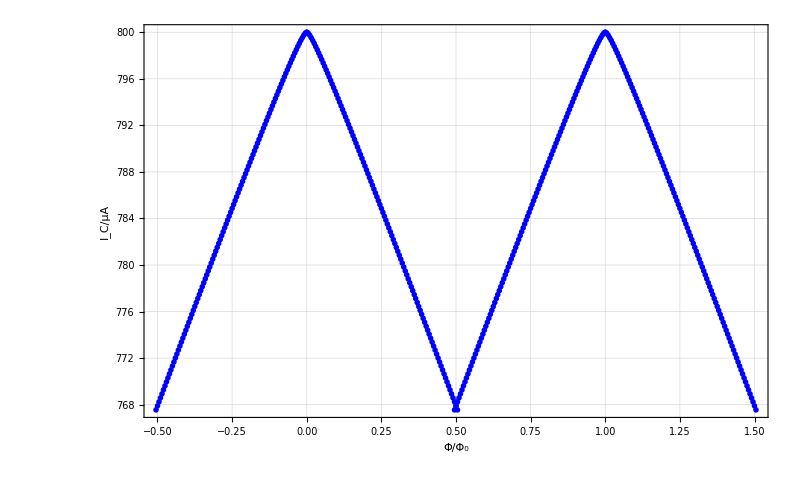

0.0413956

32.4449

```mathematica
I0=800*10^(-6);b=ϕ0/2/π/L/I0;
P1=Icflux[0,0,b,1,13.5,0,3,3,Blue,0];
ShowLegend[Show[P1,FrameLabel->{"Φ/Φ_0","I_C/μA"}],{{{Graphics[{Blue,line}],Style["L=28pH",14]}},LegendPosition->{1.1,-0.2},LegendShadow->None,LegendSize->0.35}]
tabler=tabler[[All,2]];
m=Max[tabler];
n=Min[tabler];
r=2*(m-n)/(m+n)
r1=(m-n)
```

```mathematica
b
```

0.117538